```mathematica
0.3*(1+0.5)^3/(0.3*(1.5)^3+0.7)
```

0.591241

```mathematica
0.7/(0.3*(1.5)^3+0.7)
```

0.408759

```mathematica
Sinh[0]
```

0

```mathematica
70/3.08/10^19
```

2.27273×10^-18

```mathematica
NSolve[(0.3/0.7)^(1/3)*(Sinh[1.5*Sqrt[0.7]*2.273*10^(-18)*t])^(2/3)==1,t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→4.24153×10^17}}

```mathematica
4.242*10^(17)/365/24/3600
```

1.34513×10^10

```mathematica
0.345*10^(10)*365*24*3600
```

1.08799×10^17

```mathematica
(0.3/0.7)^(1/3)*(Sinh[1.5*Sqrt[0.7]*2.273*10^(-18)*1.088*10^(17)])^(2/3)
```

0.349317

```mathematica
1/0.3493
```

2.86287

```mathematica
DSolve[a[t]*a'[t]^2==H0,a[t],t]
```

{{a(t)→(3/2)^(2/3) (-√H0 t+1)^(2/3)},{a(t)→(3/2)^(2/3) (√H0 t+1)^(2/3)}}

```mathematica
Integrate[(t/t0)^(-2/3),{t,t1,t0}]
```

ConditionalExpression[3 t0-3 t0 (t1/t0)^(1/3), ]

```mathematica
D[(Sinh[k*t])^(2/3),t]/(Sinh[k*t])^(2/3)
```

2/3 k coth(k t)

```mathematica
Coth[ArcSinh[x]]
```

(√(x^2+1))/x

```mathematica
H1[z_]:=Sqrt[0.7]*Sqrt[(0.7/0.3)*(1+z)^(-3)+1]/(0.3/0.7)^(-1/2)/(1+z)^(-3/2);
```

```mathematica
Chi1[z_]:=Integrate[1/H1[x],{x,0,z}];
```

```mathematica
Chi1[8]
```

2.08819

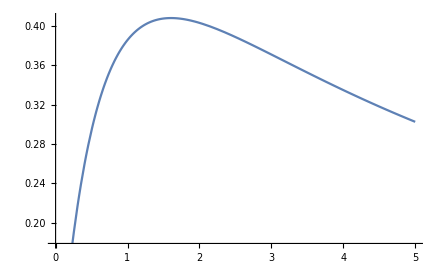

```mathematica
Plot[Chi1[m]/(1+m),{m,0,5}]
```

```mathematica
H2[z_]:=(1+z)^(3/2);
Chi2[z_]:=Integrate[1/H2[x],{x,0,z}];
```

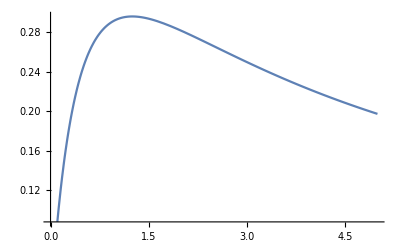

```mathematica
Plot[Chi2[m]/(1+m),{m,0,5}]
```

```mathematica
(*Plot the luminosity and angular distances vs redshift*)
```

```mathematica
a1=Plot[{Chi2[m]/(1+m),Chi2[m]*(1+m),Chi1[m]/(1+m),Chi1[m]*(1+m)},{m,0,10},AxesLabel->{"z","Distance(z) in units of c/H0"},PlotLabel-> "d_L(z) and d_A(z) for matter-Λ universe and Λ dominated universe",PlotLegends-> {"d_A(z) Λ dominated","d_L(z) Λ dominated","d_A(z) matter-Λ","d_L(z) matter-Λ"},PlotRange->{{0,10},{0,0.5}}];
```

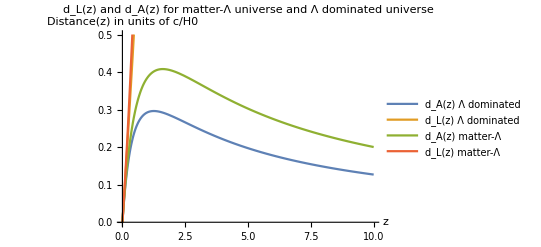

```mathematica
%368
```

```mathematica
Integrate[x/(Exp[x]+1),{x,0,Infinity}]
```

π^2/12

```mathematica
0.8/0.235*10^9*3*10^(-10)
```

1.02128

```mathematica
3Zeta[3]/2/Pi^2*(4/11*2.725)^3
```

0.177753

```mathematica
1.25^3
```

1.95313

```mathematica
Zeta[3]
```

3

```mathematica
N[Zeta[3]]
```

1.20206

```mathematica
Zeta[4]
```

π^4/90

```mathematica
2Zeta[3]/Pi^2*(2.73)^3
```

4.95614

```mathematica
410/11*3
```

1230/11

```mathematica
N[1230/11]
```

111.818

```mathematica
90*Zeta[3]/11/Pi^4/2.73*2.5*10^(-5)
```

9.24598×10^-7

```mathematica
1/(9.24598*10^(-7))
```

1.08155×10^6

```mathematica
108155/11605
```

21631/2321

```mathematica
N[21631/2321]
```

9.31969

```mathematica
N[215914/2321]
```

93.0263

```mathematica
D[1/(a*(1+x)^3+b+(1-a-b)*(1+x)^2)^(1/2),{x,3}]
```

-(15 (2 (x+1) (-a-b+1)+3 a (x+1)^2)^3)/(8 ((x+1)^2 (-a-b+1)+a (x+1)^3+b)^(7/2))+(9 (2 (-a-b+1)+6 a (x+1)) (2 (x+1) (-a-b+1)+3 a (x+1)^2))/(4 ((x+1)^2 (-a-b+1)+a (x+1)^3+b)^(5/2))-(3 a)/(((x+1)^2 (-a-b+1)+a (x+1)^3+b)^(3/2))

```mathematica
(27 a^2 (x+1)^4)/(4 (a (x+1)^3+b)^(5/2))-(3 a (x+1))/((a (x+1)^3+b)^(3/2))
```

```mathematica
-15(2+0.3-1.4)^3/8+9(2+1.2-1.4)(2+0.3-1.4)/4-0.9
```

1.37813

```mathematica
Chifull[z_]:=Integrate[1/(0.3*(1+x)^3+0.7)^(1/2),{x,0,z}];
```

```mathematica
Chiapr[z_]:=z-0.9/4*z^2+1.37813/6*z^3;
```

0.771427

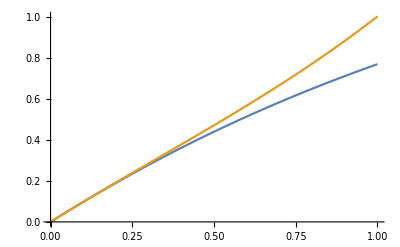

```mathematica
Plot[{Chifull[q],Chiapr[q]},{q,0,1}]
```

```mathematica
NSolve[Abs[Chifull[z]-Chiapr[z]]/Chifull[z]==0.1,z,Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{z→7.98905×10^-15},{z→0.589431}}

```mathematica
Chifull[0.01]
```

0.00997745

```mathematica
Chifull[0.1]
Chifull[0.2]
Chifull[0.3]
```

0.097707

0.190701

0.278886

```mathematica
Chifit[Ωm_,Ωu_,h_,z_]:=1/h*Integrate[1/(Ωm(1+x)^3+Ωu+(1-Ωm-Ωu)*(1+x)^2)^(1/2),{x,0,z}];
Chifit1[Ωm_,Ωu_,h_,z_]:=1/h*(z-(2+Ωm-2Ωu)/4*z^2+1/6*(-15(2+Ωm-2Ωu)^3/8+9(2+4Ωm-2Ωu)(2+Ωm-2Ωu)/4-3Ωm)*z^3);
```

General::munfl: exp(-2.45408×10^9) is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Chifit1[0.3,0.7,0.7,0.01]
Chifit1[0.3,0.7,0.7,0.1]
Chifit1[0.3,0.7,0.7,0.2]
Chifit1[0.3,0.7,0.7,0.3]
```

0.0142539

0.139971

0.275482

0.408502

```mathematica
(*z=0.01****************************************************************************************************************)
LogL1[Ωm_,Ωu_,h_,m_]:=Log[1/(0.01*Sqrt[2Pi]*Chifit1[Ωm,Ωu,h,0.01])]-(m-Chifit1[Ωm,Ωu,h,0.01])^2/2/(0.01*Chifit1[Ωm,Ωu,h,0.01])^2;
Integrate[(-D[LogL1[Ωm,Ωu,h,m],{{Ωm,Ωu,h},2}]/.{Ωm->0.3,Ωu->0.7,h->0.7})*L[0.3,0.7,0.7,m],{m,-Infinity,Infinity}]
```

Infinity::indet: Indeterminate expression 0. ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(0.0590048 | -0.120505 | 34.7047
-0.120505 | 0.246107 | -70.8773
34.7047 | -70.8773 | 20412.2)

```mathematica
Det[{{0.0590048,-0.120505,34.7047},{-0.120505,0.246107,-70.8773},{34.7047,-70.8773,20412.2}}]
```

```mathematica
-1.0150020001260864*^-9
```

```mathematica
(*This matrix is highly singular, so an inversion does not lend us much insight. Physically, this tells us that we have too much freedom in terms of fitting the parameter when z is small, even with a fairly good precision in the chi measurement*)
```

```mathematica
Inverse[{{0.0590048,-0.120505,34.7047},{-0.120505,0.246107,-70.8773},{34.7047,-70.8773,20412.2}}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix (0.0590048 | -0.120505 | 34.7047
-0.120505 | 0.246107 | -70.8773
34.7047 | -70.8773 | 20412.2) may contain significant numerical errors.

```mathematica
({{6.256036933855842*^6, 3.2239443861683956*^6, 558.028456677203}, {3.2239443861007574*^6, -1.5531693531643148*^6, -10874.40221687736}, {558.0284564423408, -10874.402216992356, -38.707904019494556}})
```

```mathematica
(*z=0.1*****************************************************************************************************************)
```

```mathematica
LogL2[Ωm_,Ωu_,h_,m_]:=Log[1/(0.01*Sqrt[2Pi]*Chifit1[Ωm,Ωu,h,0.1])]-(m-Chifit1[Ωm,Ωu,h,0.1])^2/2/(0.01*Chifit1[Ωm,Ωu,h,0.1])^2;
```

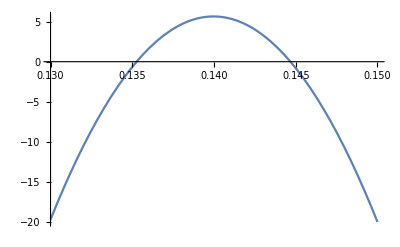

```mathematica
Plot[LogL[0.3,0.7,0.7,m],{m,0.13,0.15}]
```

```mathematica
Integrate[(-D[LogL2[Ωm,Ωu,h,m],{{Ωm,Ωu,h},2}]/.{Ωm->0.3,Ωu->0.7,h->0.7})*L[0.3,0.7,0.7,m],{m,-Infinity,Infinity}]
```

Infinity::indet: Indeterminate expression 0. ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(11.7245 | -2.10271 | -20.5063+2.51148×10^-11 ⅈ
-2.10271 | -38.6761 | 53.1316
-20.5063+2.51148×10^-11 ⅈ | 53.1316 | 211.66-2.59261×10^-10 ⅈ)

```mathematica
Inverse[{{11.7245,-2.10271,-20.5063},{-2.10271,-38.6761,53.1316},{-20.5063,53.1316,211.66}}]
```

```mathematica
({{0.10084682477886468, 0.005903548162307368, 0.008288435620440236}, {0.0059035481623073765, -0.018880233115023244, 0.0053113338536090555}, {0.008288435620440245, 0.005311333853609055, 0.004194299733473584}})
```

```mathematica
Sqrt[0.10085]/0.3
Sqrt[0.004194]/0.7
```

1.05856

0.0925159

```mathematica
(*z=0.2*****************************************************************************************************************)
```

```mathematica
LogL3[Ωm_,Ωu_,h_,m_]:=Log[1/(0.01*Sqrt[2Pi]*Chifit1[Ωm,Ωu,h,0.2])]-(m-Chifit1[Ωm,Ωu,h,0.2])^2/2/(0.01*Chifit1[Ωm,Ωu,h,0.2])^2;
```

```mathematica
Integrate[(-D[LogL3[Ωm,Ωu,h,m],{{Ωm,Ωu,h},2}]/.{Ωm->0.3,Ωu->0.7,h->0.7})*L[0.3,0.7,0.7,m],{m,-Infinity,Infinity}]
```

Infinity::indet: Indeterminate expression 0. ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(26.3841 | -6.06042 | -13.3161
-6.06042 | -83.0223 | 54.8106-6.71296×10^-11 ⅈ
-13.3161 | 54.8106-6.71296×10^-11 ⅈ | 54.6422-6.69307×10^-11 ⅈ)

```mathematica
Inverse[{{26.3841,-6.06042,-13.3161},{-6.06042,-83.0223,54.8106},{-13.3161,54.8106,54.6422}}]
```

(0.0425083 | 0.00224759 | 0.0081046
0.00224759 | -0.00712744 | 0.00769714
0.0081046 | 0.00769714 | 0.0125551)

```mathematica
Sqrt[0.0425]/0.3
```

0.687184

```mathematica
Sqrt[0.01255]/0.7
```

0.160038

```mathematica
(*z=0.3*****************************************************************************************************************)
LogL4[Ωm_,Ωu_,h_,m_]:=Log[1/(0.01*Sqrt[2Pi]*Chifit1[Ωm,Ωu,h,0.3])]-(m-Chifit1[Ωm,Ωu,h,0.3])^2/2/(0.01*Chifit1[Ωm,Ωu,h,0.3])^2;
```

```mathematica
Inverse[Integrate[(-D[LogL4[Ωm,Ωu,h,m],{{Ωm,Ωu,h},2}]/.{Ωm->0.3,Ωu->0.7,h->0.7})*L[0.3,0.7,0.7,m],{m,-Infinity,Infinity}]]
```

Infinity::indet: Indeterminate expression 0. ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(0.0240045 | -0.000633016 | 0.00384216
-0.000633016 | -0.00445698 | 0.00835082
0.00384216 | 0.00835082 | 0.0218337)

```mathematica
Sqrt[0.024]/0.3
Sqrt[0.0218]/0.7
```

0.516398

0.210926

```mathematica
LogL1[Ωm_,Ωu_,h_,m_]:=Log[1/(0.01*Sqrt[2Pi]*Chifit[Ωm,Ωu,h,0.2])]-(m-Chifit[Ωm,Ωu,h,0.2])^2/2/(0.01*Chifit[Ωm,Ωu,h,0.2])^2;
Integrate[(-D[LogL1[Ωm,Ωu,h,m],{{Ωm,Ωu,h},2}]/.{Ωm->0.3,Ωu->0.7,h->0.7})*L[0.3,0.7,0.7,m],{m,-Infinity,Infinity}]
```

$Aborted